## Introduction

We look at periodic orbit structures of cat maps with form
f[x]=A.x mod 1, A=(a | 1
a b-1 | b),
where x is a 2-d vector on the unit square (torus) [0,1)×[0,1) and a,b are integers. As the cat map is piecewise linear and the matrix A has integer entries, all of its periodic points have rational coordinates.

The total number of length-k periodic orbits (all, not the prime ones, or the total number of fixed points of f^(k)) is Tr[A^k]-2=A_1^k+A_2^k-2≡N_k, where A_(1,2) are the eigenvalues of A. As a result, the topological zeta function of the single cat map is
1/ζ_topo[z]=Exp[-∑_k N_k/k z^k]=Exp[-∑_k (Tr[A^k]-2)/k z^k]=Det[I-A z]/(1-z)^2,
which is a rational function.

### Definitions

The matrix A and the vertices of unit square:

```mathematica
A:={{a,1},{a b-1,b}};
Sq01={{0,0},{1,0},{1,1},{0,1}};
```

Conversions between number of fixed points and prime periodic orbits (mainly used to check the validity of fixed point numbers):

```mathematica
PToF[ps_]:=Module[{fs={ps[[1]]},i,ids},Do[ids=Divisors[i]//Most;AppendTo[fs,ps[[i]] i+ps[[ids]].ids],{i,2,Length[ps]}];fs];
FToP[fs_]:=Module[{ps={fs[[1]]},i,ids},Do[ids=Divisors[i]//Most;AppendTo[ps,(fs[[i]]-ps[[ids]].ids)/i],{i,2,Length[fs]}];ps];
```

## {a,b}={2,1}

### Graph of the mapping

```mathematica
{a,b}={2,1};
A//Eigenvalues
%//N
```

{1/2 (3+√5),1/2 (3-√5)}

{2.61803,0.381966}

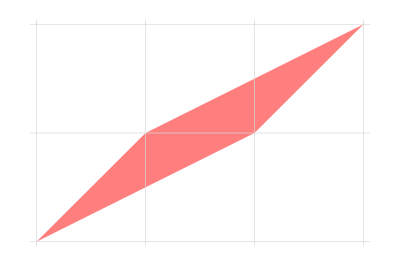

```mathematica
Graphics[{Red,Opacity[.5],Polygon[A.# &/@Sq01]},GridLines->{Range[0,10],Range[0,10]}]
```

We see that after one mapping, the unit square is stretched into 4 squares, which are displaced from the original one by the following list:

```mathematica
r0s={{0,0},{1,0},{1,1},{2,1}};
```

They can be later used to find all periodic points of the cat map with a given length. The most straightforward way is to list all 4^k possible combinations (words) of the displacements, solve the inhomogeneous equation f^(k)[x]=x, and discard those solutions outside of the original unit square. For large k this will be much less efficient as the actual admissible orbits grow with an exponent of the largest eigenvalue of A, which is less than 4 (≈2.618).

### Number of periodic orbits (fixed points)

The theory value:

```mathematica
fs=Tr[MatrixPower[A,#]]-2 &/@Range[20]
```

{1,5,16,45,121,320,841,2205,5776,15125,39601,103680,271441,710645,1860496,4870845,12752041,33385280,87403801,228826125}

Finding the number of periodic orbits: Note that the function BinLists[] does not count those points having coordinates 1, which happens to be good for our purpose as 1 and 0 are identified as the same point.

```mathematica
{x,y}/.Solve[Fold[Simplify[A.#1-#2]&,{x,y},#]=={x,y},{x,y}][[1]]&/@Tuples[r0s,1]
```

{{0,0},{0,1},{1,0},{1,1}}

```mathematica
Do[Print["length = ",k,"\t",Flatten[BinLists[Parallelize[{x,y}/.Solve[Fold[Simplify[A.#1-#2]&,{x,y},#]=={x,y},{x,y}][[1]]&/@Tuples[r0s,k]],{0,1},{0,1}],2]//CountDistinct],{k,9}]
```

length = 1	1

length = 2	5

length = 3	16

length = 4	45

length = 5	121

length = 6	320

length = 7	841

length = 8	2205

length = 9	5776

### Number of prime periodic orbits

```mathematica
ps=FToP[fs]
```

{1,2,5,10,24,50,120,270,640,1500,3600,8610,20880,50700,124024,304290,750120,1854400,4600200,11440548}

### Topological zeta function

Verify that 1/ζ_topo[z]=Det[I-A z]/(1-z)^2:

```mathematica
m=Length[fs];
Series[Exp[-fs.(z^#/#&/@Range[m])],{z,0,m}]
Series[Det[IdentityMatrix[2]-A z]/(1-z)^2,{z,0,m}]
%-%%
Clear[m];
```

1-z-2 z^2-3 z^3-4 z^4-5 z^5-6 z^6-7 z^7-8 z^8-9 z^9-10 z^10-11 z^11-12 z^12-13 z^13-14 z^14-15 z^15-16 z^16-17 z^17-18 z^18-19 z^19-20 z^20+O[z]^21

1-z-2 z^2-3 z^3-4 z^4-5 z^5-6 z^6-7 z^7-8 z^8-9 z^9-10 z^10-11 z^11-12 z^12-13 z^13-14 z^14-15 z^15-16 z^16-17 z^17-18 z^18-19 z^19-20 z^20+O[z]^21

O[z]^21

## {a,b}={3,1}

### Graph of the mapping

```mathematica
{a,b}={3,1};
A//Eigenvalues
%//N
```

{2+√3,2-√3}

{3.73205,0.267949}

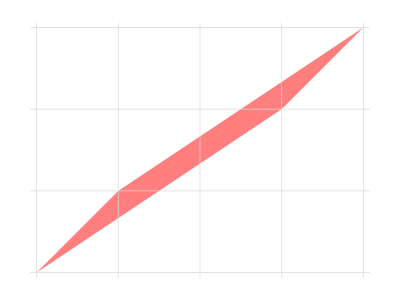

```mathematica
Graphics[{Red,Opacity[.5],Polygon[A.# &/@Sq01]},GridLines->{Range[0,10],Range[0,10]}]
```

The unit square is stretched into 6 squares, and there are 6 symbols accordingly.

```mathematica
r0s={{0,0},{1,0},{1,1},{2,1},{2,2},{3,2}};
```

### Number of periodic orbits (fixed points)

The theory value:

```mathematica
fs=Tr[MatrixPower[A,#]]-2 &/@Range[20]
```

{2,12,50,192,722,2700,10082,37632,140450,524172,1956242,7300800,27246962,101687052,379501250,1416317952,5285770562,19726764300,73621286642,274758382272}

```mathematica
{x,y}/.Solve[Fold[Simplify[A.#1-#2]&,{x,y},#]=={x,y},{x,y}][[1]]&/@Tuples[r0s,1]
```

{{0,0},{0,1},{1/2,0},{1/2,1},{1,0},{1,1}}

```mathematica
Do[Print["length = ",k,"\t",Flatten[BinLists[Parallelize[{x,y}/.Solve[Fold[Simplify[A.#1-#2]&,{x,y},#]=={x,y},{x,y}][[1]]&/@Tuples[r0s,k]],{0,1},{0,1}],2]//CountDistinct],{k,8}]
```

length = 1	2

length = 2	12

length = 3	50

length = 4	192

length = 5	722

length = 6	2700

length = 7	10082

length = 8	37632

### Number of prime periodic orbits

```mathematica
ps=FToP[fs]
```

{2,5,16,45,144,440,1440,4680,15600,52344,177840,608160,2095920,7262640,25300032,88517520,310927680,1095923400,3874804560,13737892896}

### Topological zeta function

Verify that 1/ζ_topo[z]=Det[I-A z]/(1-z)^2:

```mathematica
m=Length[fs];
Series[Exp[-fs.(z^#/#&/@Range[m])],{z,0,m}]
Series[Det[IdentityMatrix[2]-A z]/(1-z)^2,{z,0,m}]
%-%%
Clear[m];
```

1-2 z-4 z^2-6 z^3-8 z^4-10 z^5-12 z^6-14 z^7-16 z^8-18 z^9-20 z^10-22 z^11-24 z^12-26 z^13-28 z^14-30 z^15-32 z^16-34 z^17-36 z^18-38 z^19-40 z^20+O[z]^21

1-2 z-4 z^2-6 z^3-8 z^4-10 z^5-12 z^6-14 z^7-16 z^8-18 z^9-20 z^10-22 z^11-24 z^12-26 z^13-28 z^14-30 z^15-32 z^16-34 z^17-36 z^18-38 z^19-40 z^20+O[z]^21

O[z]^21